```mathematica
2+2
```

4

```mathematica
%+3
```

7

```mathematica
%+3
```

10

```mathematica
GCD[17^3,17^6*2^7]
```

4913

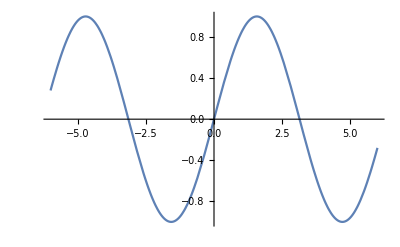

```mathematica
Plot[Sin[x], {x, -6., 6.}]
```

```mathematica
{1,2,3}
{x,y,z}
```

{1,2,3}

{x,y,z}

```mathematica
{1,2,3}+2
```

{3,4,5}

```mathematica
Range[10]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
{a,b,c,d}[[3]]
```

c

```mathematica
Sin[x]/Cos[x]
```

Tan[x]

```mathematica
Solve[{Tan[x]==1,0<x<2 Pi}]
```

{{x→π/4},{x→(5 π)/4}}

```mathematica
FindRoot[Cos[x^2+3.1212]==x,{x,0}]
```

{x→-0.807268}

```mathematica
Find[aa*x^2+bb*x+cc,{x,0}]
```

Find::stream: cc+bb x+aa x^2 is not a string, SocketObject, InputStream[ ], or OutputStream[ ].

$Failed

```mathematica
DSolve[y'''[x]==Tan[x],y[x],x]
```

{{y[x]→C[1]+x C[2]+x^2 C[3]+1/6 x^2 (-2 ⅈ x+3 Log[1+ⅇ^(2 ⅈ x)]-3 Log[Cos[x]])-1/4 PolyLog[3,-ⅇ^(2 ⅈ x)]}}

```mathematica
DSolve[D[(xi^2*th'[xi]),xi]/xi^2+(th[xi]) ==0,th[xi],xi]
```

{{th[xi]→(ⅇ^(-ⅈ xi) C[1])/xi-(ⅈ ⅇ^(ⅈ xi) C[2])/(2 xi)}}

```mathematica
Series[x*(2x^2-3)*Sqrt[x^2+1]+3*ArcSinh[x],{x,0,10}]
```

(8 x^5)/5-(4 x^7)/7+x^9/3+O[x]^11

```mathematica
10000!+100!+10!
```

```mathematica
Simplify[Integrate[8 x^4*(Cos[x])^10,x]]
```

(63 x^5)/160+105/64 x (-3+2 x^2) Cos[2 x]+15/256 x (-3+8 x^2) Cos[4 x]-5/384 x Cos[6 x]+5/64 x^3 Cos[6 x]-(15 x Cos[8 x])/16384+5/512 x^3 Cos[8 x]-(3 x Cos[10 x])/80000+(x^3 Cos[10 x])/1600+315/64 Cos[x] Sin[x]-315/64 x^2 Sin[2 x]+105/64 x^4 Sin[2 x]+(45 Sin[4 x])/1024-45/128 x^2 Sin[4 x]+15/32 x^4 Sin[4 x]+(5 Sin[6 x])/2304-5/128 x^2 Sin[6 x]+15/128 x^4 Sin[6 x]+(15 Sin[8 x])/131072-(15 x^2 Sin[8 x])/4096+5/256 x^4 Sin[8 x]+(3 Sin[10 x])/800000-(3 x^2 Sin[10 x])/16000+1/640 x^4 Sin[10 x]

```mathematica
FullSimplify[Integrate[8 x^4*(Cos[x])^10,x]]
```

(63 x^5)/160+105/64 x (-3+2 x^2) Cos[2 x]+15/256 x (-3+8 x^2) Cos[4 x]+5/384 x (-1+6 x^2) Cos[6 x]+(5 x (-3+32 x^2) Cos[8 x])/16384+(x (-3+50 x^2) Cos[10 x])/80000+105/64 (3-6 x^2+2 x^4) Cos[x] Sin[x]+(15 (3-24 x^2+32 x^4) Sin[4 x])/1024+(5 (1-18 x^2+54 x^4) Sin[6 x])/2304+(5 (3-96 x^2+512 x^4) Sin[8 x])/131072+((3+50 x^2 (-3+25 x^2)) Sin[10 x])/800000

```mathematica
Apart[(63 x^5)/160+105/64 x (-3+2 x^2) Cos[2 x]+15/256 x (-3+8 x^2) Cos[4 x]+5/384 x (-1+6 x^2) Cos[6 x]+(5 x (-3+32 x^2) Cos[8 x])/16384+(x (-3+50 x^2) Cos[10 x])/80000+105/64 (3-6 x^2+2 x^4) Cos[x] Sin[x]+(15 (3-24 x^2+32 x^4) Sin[4 x])/1024+(5 (1-18 x^2+54 x^4) Sin[6 x])/2304+(5 (3-96 x^2+512 x^4) Sin[8 x])/131072+((3+50 x^2 (-3+25 x^2)) Sin[10 x])/800000]
```

1/737280000(290304000 x^5-3628800000 x Cos[2 x]+2419200000 x^3 Cos[2 x]-129600000 x Cos[4 x]+345600000 x^3 Cos[4 x]-9600000 x Cos[6 x]+57600000 x^3 Cos[6 x]-675000 x Cos[8 x]+7200000 x^3 Cos[8 x]-27648 x Cos[10 x]+460800 x^3 Cos[10 x]+3628800000 Cos[x] Sin[x]-7257600000 x^2 Cos[x] Sin[x]+2419200000 x^4 Cos[x] Sin[x]+32400000 Sin[4 x]-259200000 x^2 Sin[4 x]+345600000 x^4 Sin[4 x]+1600000 Sin[6 x]-28800000 x^2 Sin[6 x]+86400000 x^4 Sin[6 x]+84375 Sin[8 x]-2700000 x^2 Sin[8 x]+14400000 x^4 Sin[8 x])+((3-150 x^2+1250 x^4) Sin[10 x])/800000

```mathematica
Apart[(a+b)/(a*b)]
```

1/a+1/b

```mathematica
Together[1/a+1/b]
```

(a+b)/(a b)